# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-20

```mathematica
states=Union[seqData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Alabama→{{2022-01-06,11},{2022-01-07,31},{2022-01-08,5},{2022-01-09,1},{2022-01-10,6},{2022-01-11,35},{2022-01-12,24},{2022-01-13,26},{2022-01-14,7},{2022-01-15,0},{2022-01-16,3},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0}},Arizona→{{2022-01-06,569},{2022-01-07,355},{2022-01-08,255},{2022-01-09,426},{2022-01-10,423},{2022-01-11,417},{2022-01-12,458},{2022-01-13,312},{2022-01-14,192},{2022-01-15,30},{2022-01-16,317},{2022-01-17,227},{2022-01-18,161},{2022-01-19,303},{2022-01-20,39}},Arkansas→{{2022-01-06,89},{2022-01-07,76},{2022-01-08,3},{2022-01-09,10},{2022-01-10,147},{2022-01-11,103},{2022-01-12,46},{2022-01-13,6},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0}},California→{{2022-01-06,312},{2022-01-07,421},{2022-01-08,121},{2022-01-09,148},{2022-01-10,402},{2022-01-11,259},{2022-01-12,196},{2022-01-13,95},{2022-01-14,75},{2022-01-15,450},{2022-01-16,33},{2022-01-17,1011},{2022-01-18,696},{2022-01-19,15},{2022-01-20,11}},Colorado→{{2022-01-06,468},{2022-01-07,1115},{2022-01-08,781},{2022-01-09,262},{2022-01-10,544},{2022-01-11,339},{2022-01-12,378},{2022-01-13,52},{2022-01-14,1},{2022-01-15,1},{2022-01-16,33},{2022-01-17,3},{2022-01-18,12},{2022-01-19,0},{2022-01-20,1}},Connecticut→{{2022-01-06,236},{2022-01-07,175},{2022-01-08,114},{2022-01-09,157},{2022-01-10,52},{2022-01-11,55},{2022-01-12,52},{2022-01-13,32},{2022-01-14,49},{2022-01-15,18},{2022-01-16,14},{2022-01-17,21},{2022-01-18,83},{2022-01-19,102},{2022-01-20,102}},Delaware→{{2022-01-06,192},{2022-01-07,72},{2022-01-08,5},{2022-01-09,7},{2022-01-10,64},{2022-01-11,75},{2022-01-12,36},{2022-01-13,50},{2022-01-14,53},{2022-01-15,1},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0}},Florida→{{2022-01-06,148},{2022-01-07,111},{2022-01-08,113},{2022-01-09,108},{2022-01-10,182},{2022-01-11,155},{2022-01-12,141},{2022-01-13,87},{2022-01-14,31},{2022-01-15,1},{2022-01-16,2},{2022-01-17,16},{2022-01-18,17},{2022-01-19,10},{2022-01-20,0}},Georgia→{{2022-01-06,11},{2022-01-07,19},{2022-01-08,33},{2022-01-09,38},{2022-01-10,127},{2022-01-11,142},{2022-01-12,97},{2022-01-13,97},{2022-01-14,51},{2022-01-15,1},{2022-01-16,0},{2022-01-17,27},{2022-01-18,151},{2022-01-19,0},{2022-01-20,0}},Hawaii→{{2022-01-06,7},{2022-01-07,27},{2022-01-08,17},{2022-01-09,12},{2022-01-10,25},{2022-01-11,33},{2022-01-12,12},{2022-01-13,12},{2022-01-14,14},{2022-01-15,14},{2022-01-16,6},{2022-01-17,8},{2022-01-18,15},{2022-01-19,16},{2022-01-20,7}},Illinois→{{2022-01-06,42},{2022-01-07,48},{2022-01-08,53},{2022-01-09,50},{2022-01-10,112},{2022-01-11,90},{2022-01-12,55},{2022-01-13,49},{2022-01-14,36},{2022-01-15,7},{2022-01-16,22},{2022-01-17,31},{2022-01-18,36},{2022-01-19,12},{2022-01-20,10}},Indiana→{{2022-01-06,58},{2022-01-07,47},{2022-01-08,25},{2022-01-09,38},{2022-01-10,71},{2022-01-11,76},{2022-01-12,74},{2022-01-13,58},{2022-01-14,14},{2022-01-15,1},{2022-01-16,0},{2022-01-17,9},{2022-01-18,13},{2022-01-19,19},{2022-01-20,9}},Louisiana→{{2022-01-06,151},{2022-01-07,65},{2022-01-08,20},{2022-01-09,18},{2022-01-10,31},{2022-01-11,17},{2022-01-12,42},{2022-01-13,46},{2022-01-14,18},{2022-01-15,23},{2022-01-16,1},{2022-01-17,8},{2022-01-18,8},{2022-01-19,7},{2022-01-20,6}},Maryland→{{2022-01-06,172},{2022-01-07,131},{2022-01-08,95},{2022-01-09,85},{2022-01-10,138},{2022-01-11,162},{2022-01-12,122},{2022-01-13,72},{2022-01-14,37},{2022-01-15,36},{2022-01-16,30},{2022-01-17,25},{2022-01-18,19},{2022-01-19,17},{2022-01-20,9}},Massachusetts→{{2022-01-06,1076},{2022-01-07,608},{2022-01-08,464},{2022-01-09,1371},{2022-01-10,1173},{2022-01-11,806},{2022-01-12,799},{2022-01-13,708},{2022-01-14,845},{2022-01-15,318},{2022-01-16,325},{2022-01-17,808},{2022-01-18,740},{2022-01-19,624},{2022-01-20,497}},Michigan→{{2022-01-06,58},{2022-01-07,34},{2022-01-08,43},{2022-01-09,36},{2022-01-10,105},{2022-01-11,42},{2022-01-12,61},{2022-01-13,66},{2022-01-14,44},{2022-01-15,6},{2022-01-16,11},{2022-01-17,14},{2022-01-18,3},{2022-01-19,3},{2022-01-20,0}},Minnesota→{{2022-01-06,103},{2022-01-07,183},{2022-01-08,50},{2022-01-09,54},{2022-01-10,119},{2022-01-11,221},{2022-01-12,62},{2022-01-13,39},{2022-01-14,33},{2022-01-15,22},{2022-01-16,27},{2022-01-17,26},{2022-01-18,5},{2022-01-19,2},{2022-01-20,0}},Nebraska→{{2022-01-06,56},{2022-01-07,56},{2022-01-08,44},{2022-01-09,25},{2022-01-10,77},{2022-01-11,77},{2022-01-12,96},{2022-01-13,106},{2022-01-14,34},{2022-01-15,14},{2022-01-16,31},{2022-01-17,38},{2022-01-18,87},{2022-01-19,29},{2022-01-20,66}},Nevada→{{2022-01-06,55},{2022-01-07,52},{2022-01-08,31},{2022-01-09,28},{2022-01-10,104},{2022-01-11,73},{2022-01-12,23},{2022-01-13,51},{2022-01-14,21},{2022-01-15,1},{2022-01-16,3},{2022-01-17,17},{2022-01-18,9},{2022-01-19,37},{2022-01-20,20}},New Jersey→{{2022-01-06,119},{2022-01-07,65},{2022-01-08,26},{2022-01-09,25},{2022-01-10,118},{2022-01-11,384},{2022-01-12,379},{2022-01-13,56},{2022-01-14,62},{2022-01-15,7},{2022-01-16,11},{2022-01-17,10},{2022-01-18,7},{2022-01-19,1},{2022-01-20,1}},New Mexico→{{2022-01-06,108},{2022-01-07,84},{2022-01-08,17},{2022-01-09,11},{2022-01-10,69},{2022-01-11,54},{2022-01-12,25},{2022-01-13,10},{2022-01-14,9},{2022-01-15,2},{2022-01-16,1},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0}},New York→{{2022-01-06,412},{2022-01-07,258},{2022-01-08,448},{2022-01-09,391},{2022-01-10,527},{2022-01-11,633},{2022-01-12,290},{2022-01-13,147},{2022-01-14,17},{2022-01-15,0},{2022-01-16,6},{2022-01-17,10},{2022-01-18,30},{2022-01-19,8},{2022-01-20,25}},North Carolina→{{2022-01-06,94},{2022-01-07,156},{2022-01-08,122},{2022-01-09,137},{2022-01-10,242},{2022-01-11,235},{2022-01-12,136},{2022-01-13,69},{2022-01-14,80},{2022-01-15,49},{2022-01-16,27},{2022-01-17,20},{2022-01-18,54},{2022-01-19,89},{2022-01-20,0}},North Dakota→{{2022-01-06,19},{2022-01-07,63},{2022-01-08,24},{2022-01-09,88},{2022-01-10,29},{2022-01-11,124},{2022-01-12,36},{2022-01-13,32},{2022-01-14,51},{2022-01-15,123},{2022-01-16,30},{2022-01-17,22},{2022-01-18,7},{2022-01-19,21},{2022-01-20,2}},Ohio→{{2022-01-06,123},{2022-01-07,99},{2022-01-08,4},{2022-01-09,3},{2022-01-10,118},{2022-01-11,81},{2022-01-12,62},{2022-01-13,56},{2022-01-14,55},{2022-01-15,0},{2022-01-16,0},{2022-01-17,1},{2022-01-18,56},{2022-01-19,3},{2022-01-20,0}},Oregon→{{2022-01-06,209},{2022-01-07,207},{2022-01-08,115},{2022-01-09,34},{2022-01-10,99},{2022-01-11,78},{2022-01-12,82},{2022-01-13,38},{2022-01-14,7},{2022-01-15,1},{2022-01-16,1},{2022-01-17,31},{2022-01-18,26},{2022-01-19,26},{2022-01-20,7}},Pennsylvania→{{2022-01-06,65},{2022-01-07,44},{2022-01-08,16},{2022-01-09,21},{2022-01-10,48},{2022-01-11,253},{2022-01-12,170},{2022-01-13,31},{2022-01-14,9},{2022-01-15,30},{2022-01-16,2},{2022-01-17,2},{2022-01-18,2},{2022-01-19,1},{2022-01-20,0}},South Carolina→{{2022-01-06,4},{2022-01-07,11},{2022-01-08,13},{2022-01-09,2},{2022-01-10,66},{2022-01-11,134},{2022-01-12,73},{2022-01-13,14},{2022-01-14,2},{2022-01-15,0},{2022-01-16,0},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0}},Tennessee→{{2022-01-06,28},{2022-01-07,33},{2022-01-08,70},{2022-01-09,23},{2022-01-10,53},{2022-01-11,37},{2022-01-12,37},{2022-01-13,24},{2022-01-14,46},{2022-01-15,0},{2022-01-16,1},{2022-01-17,0},{2022-01-18,0},{2022-01-19,0},{2022-01-20,0}},Texas→{{2022-01-06,584},{2022-01-07,94},{2022-01-08,44},{2022-01-09,36},{2022-01-10,115},{2022-01-11,49},{2022-01-12,40},{2022-01-13,28},{2022-01-14,14},{2022-01-15,0},{2022-01-16,3},{2022-01-17,0},{2022-01-18,2},{2022-01-19,2},{2022-01-20,0}},Utah→{{2022-01-06,244},{2022-01-07,196},{2022-01-08,151},{2022-01-09,22},{2022-01-10,403},{2022-01-11,342},{2022-01-12,255},{2022-01-13,139},{2022-01-14,183},{2022-01-15,202},{2022-01-16,18},{2022-01-17,363},{2022-01-18,169},{2022-01-19,41},{2022-01-20,0}},Vermont→{{2022-01-06,92},{2022-01-07,193},{2022-01-08,258},{2022-01-09,60},{2022-01-10,29},{2022-01-11,477},{2022-01-12,89},{2022-01-13,67},{2022-01-14,200},{2022-01-15,90},{2022-01-16,47},{2022-01-17,177},{2022-01-18,249},{2022-01-19,126},{2022-01-20,115}},Virginia→{{2022-01-06,20},{2022-01-07,46},{2022-01-08,52},{2022-01-09,53},{2022-01-10,179},{2022-01-11,153},{2022-01-12,30},{2022-01-13,9},{2022-01-14,6},{2022-01-15,0},{2022-01-16,0},{2022-01-17,0},{2022-01-18,14},{2022-01-19,1},{2022-01-20,0}},Washington→{{2022-01-06,249},{2022-01-07,318},{2022-01-08,339},{2022-01-09,166},{2022-01-10,556},{2022-01-11,211},{2022-01-12,136},{2022-01-13,160},{2022-01-14,87},{2022-01-15,1},{2022-01-16,2},{2022-01-17,61},{2022-01-18,64},{2022-01-19,15},{2022-01-20,6}},Wisconsin→{{2022-01-06,122},{2022-01-07,193},{2022-01-08,20},{2022-01-09,21},{2022-01-10,102},{2022-01-11,47},{2022-01-12,64},{2022-01-13,81},{2022-01-14,62},{2022-01-15,0},{2022-01-16,1},{2022-01-17,5},{2022-01-18,1},{2022-01-19,5},{2022-01-20,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

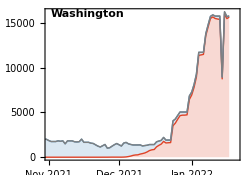

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

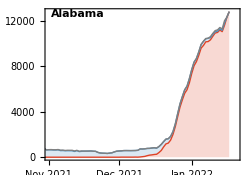
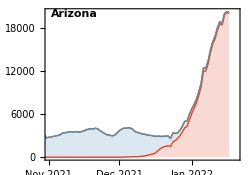
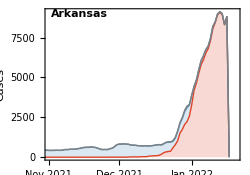
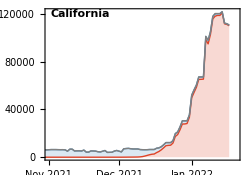
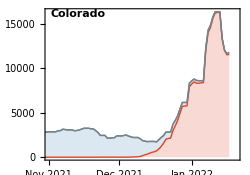
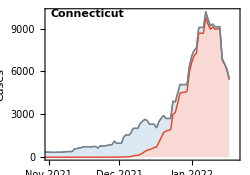
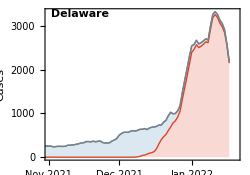
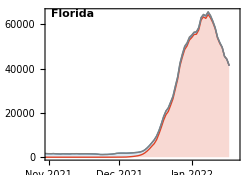
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png